```mathematica
w=Exp[-z^2] Erfc[-ⅈ z]
```

ⅇ^(-z^2) Erfc[-ⅈ z]

```mathematica
VW=1/(σ √(2 π))Re[w/.z->(x+ⅈ γ)/(σ √2)]
```

Re[ⅇ^(-(x+ⅈ γ)^2/(2 σ^2)) Erfc[-(ⅈ (x+ⅈ γ))/(√2 σ)]]/(√(2 π) σ)

```mathematica
G[x_]=1/(σ √(2π))Exp[-x^2/(2 σ^2)]
L[x_]=γ/(π(x^2+γ^2))
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)

γ/(π (x^2+γ^2))

```mathematica
VC=Convolve[G[y],L[y],y,x]
```

-1/(2 √2 π^(3/2) σ)ⅈ ⅇ^(-(x+ⅈ γ)^2/(2 σ^2)) (-π Erfi[((x+ⅈ γ) √(1/σ^2))/(√2)]-Log[-x-ⅈ γ]+ⅇ^((2 ⅈ x γ)/σ^2) (π Erfi[((x-ⅈ γ) √(1/σ^2))/(√2)]-Log[x-ⅈ γ]+Log[-x+ⅈ γ])+Log[x+ⅈ γ])

```mathematica
N[VW/.{γ->2,σ->1,x->1}]
```

0.118588

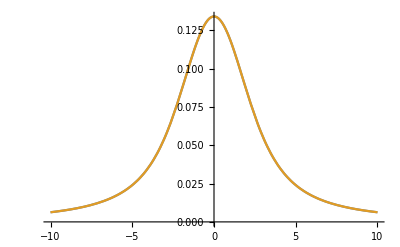

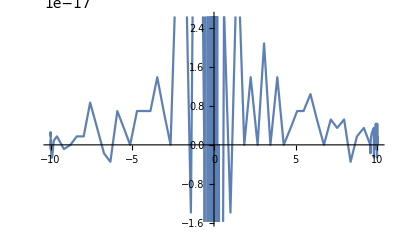

```mathematica
Plot[{Re[VW/.{γ->2,σ->1}],Re[VC/.{γ->2,σ->1}]},{x,-10,10}]
Plot[{Re[VW/.{γ->2,σ->1}]-Re[VC/.{γ->2,σ->1}]},{x,-10,10}]
```

```mathematica
FullSimplify[D[v,x]]
```

(ⅇ^(-((1+i^2) (x+ⅈγ)^2)/(2 σ^2)) (i √(2/π) σ+ⅇ^((i^2 (x+ⅈγ)^2)/(2 σ^2)) (x+ⅈγ) (-2+Erfc[(i (x+ⅈγ))/(√2 σ)])) Re'[ⅇ^(-(x+ⅈγ)^2/(2 σ^2)) (1+Erf[(i (x+ⅈγ))/(√2 σ)])])/(√(2 π) σ^3)

```mathematica
Lun[x_]=γ^2/(x^2+γ^2)
```

γ^2/(x^2+γ^2)

```mathematica
D[Lun[x],{x,1}]
D[L[x],{x,1}]
```

-(2 x γ^2)/((x^2+γ^2)^2)

-(2 x γ)/(π (x^2+γ^2)^2)

```mathematica
Gun[x_]=Exp[-x^2/(2 σ^2)]
D[Gun[x],{x,1}]
D[G[x],{x,1}]
```

ⅇ^(-x^2/(2 σ^2))

-(ⅇ^(-x^2/(2 σ^2)) x)/σ^2

-(ⅇ^(-x^2/(2 σ^2)) x)/(√(2 π) σ^3)

```mathematica
D[Exp[(-(x-μ)^2)/(2 σ^2)],{x,5}]
```

-(ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ)^5)/σ^10+(10 ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ)^3)/σ^8-(15 ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ))/σ^6

```mathematica
D[U0*Exp[(-(x-μ)^2)/(2 σ^2)]+1/2 m ω^2 x^2,{x,1}]
```

-(ⅇ^(-(x-μ)^2/(2 σ^2)) U0 (x-μ))/σ^2+m x ω^2